```mathematica
SDATA={
CI->1.5 10^6,
TW->0.170,
TL-> 1.5,
g-> 9.81,
𝒟-> TL/2,
d-> 0.410/2,
h->0.0,
d1-> 0.740,
d2-> 0.330,
d3->1.348,
r1->d1/2,
r2->d2/2,
r3->d3/2,
𝒷->0.380,
𝒹->d3,
𝒽->0.70 𝒷,
m0->212.3 ,
m1->316.3,
m2->47.5,
m4->316.3,
𝓂1->2137.84,
𝓂2->90.0,
Jz0->44.3,
Jz1-> 24.05,
Jz2->0.71,
Jz4-> 24.05,
𝒥z1->1/12 𝓂1 Δx2^2,
𝒥z2->12.676,
k-> 5.0 10^6,
kpneu-> 2.5 10^6,
b->2 2 2 2 2 4 28000.0,
bpneu->2 2 2 2 2 2 28000.0,
IF->   6 3400.0,
vd-> 2.0,
sd-> 0.047787558339910864,
ωd-> vd/(r1(1-sd)),
λ->  1.0,
vmin->0.0001,
ωmin-> vmin/r1,
vymin-> -1.0 10^-6,
l0-> 0.500,
Δy2->0.2,
Δx2->3.2,
xc->1.6  1.90,
yc->0.65,
β->0.58
};
```

```mathematica
𝒥z1//.SDATA
```

1824.29

```mathematica
m={m0,m1,m2,m2,m4};
Jz={Jz0,Jz1,Jz2,Jz2,Jz4};
M0[i_]:={{m⟦i+1⟧,0,0},{0,m⟦i+1⟧,0},{0,0,Jz⟦i+1⟧}};
r={0,1, r1/r2, r1/r2,1};
X0={0,𝒟,d,-d,-𝒟};
Y0={h,0,r2-r1,r2-r1,0};
ξ0[t_]={x0[t],y0[t],α0[t],θ0[t]};
q0[i_]:={x0[t]+Cos[α0[t]] X0⟦i+1⟧-Sin[α0[t]] Y0⟦i+1⟧,y0[t]+Sin[α0[t]] X0⟦i+1⟧+Cos[α0[t]] Y0⟦i+1⟧,α0[t] -r⟦i+1⟧ θ0[t]};
J0[i_]:=D[q0[i], {ξ0[t]}];
dJ0[i_]:=D[J0[i], t];
𝕄0=Simplify[∑_(i=0)^4 J0[i]ᵀ.M0[i].J0[i]];
𝕧0=Simplify[(∑_(i=0)^4 J0[i]ᵀ.M0[i].dJ0[i]).ξ0'[t]];
𝕘0=Simplify[(∑_(i=0)^4 J0[i]ᵀ.{0,m⟦i+1⟧g,0})];
𝕒0={a0,0,0,0};
W0 =- TW TL Cos[α0[t]](k(y0[t]-r1)+b(y0'[t]-0));
s0 = 1 - x0'[t]/(r1 θ0'[t]);
DWR = 1 - (TL Sin[2α0[t]])/(12(d1-y0[t]));
Bn0 =Simplify[ (CI TW TL)/(W0 (1-Exp[-CI/(0.698 10^6)]))5/(1+6 TW/TL)];
DWI = 1 - Abs[(0.7(DWR-1))/(DWR+1)];
GTR0 = 1.10 (1-Exp[-0.025 Bn0])(1-Exp[-17 s0])+0.03/DWI;
MRR0=2.5/(Bn0 DWI)+0.03/DWI+(0.5s0)/(√Bn0);
NTR0 = GTR0 - MRR0;
TE0 = NTR0/GTR0(1-s0);
GT0 = W0 GTR0;
MR0 = W0 MRR0;
NT0 = W0 NTR0;
𝕗0={
W0(GTR0 Tanh[100 (r1 θ0'[t]- x0'[t])]-MRR0 Tanh[100 x0'[t]] )Cos[α0[t]]-0IF Tanh[100 x0'[t]],
W0 (1+(GTR0 Tanh[100 (r1 θ0'[t]-x0'[t])]-MRR0 Tanh[100 x0'[t]] )Sin[α0[t]]),
-k TW TL^3 Cos[α0[t]]^2 Sin[α0[t]]-b TW TL^3 D[(Cos[α0[t]]^2 Sin[α0[t]]), t],
τ0[t]-r1 W0(GTR0 Tanh[100 (r1 θ0'[t]-x0'[t])]-0MRR0 Tanh[100 x0'[t]] )
};
```

```mathematica
(*Rocker Boogie*)
𝓍[t_]={
-l0 Sin[ϕ[t]],
xc,
Δx2
};
𝓎[t_]={
-l0 Cos[ϕ[t]],
yc,
-Δy2
};
X[i_]:=x[t]+(𝓍[t]⟦i+1⟧-xc) Cos[α[t]]-(𝓎[t]⟦i+1⟧-yc) Sin[α[t]];
Y[i_]:=y[t]+(𝓍[t]⟦i+1⟧-xc) Sin[α[t]]+(𝓎[t]⟦i+1⟧-yc) Cos[α[t]];
q={
{X[0],Y[0],α[t]-ϕ[t] , θ0[t]},
{X[1],Y[1],α[t] },
{X[2],Y[2],α[t]-θ2[t]}
};
SUBS0=
{
x0[t]->X[0],
y0[t]->Y[0],
α0[t]->α[t]-ϕ[t] ,
x0'[t]->D[X[0], t],
y0'[t]->D[Y[0], t],
α0'[t]->α'[t]-ϕ'[t] 
};
ξ[t_]={x[t], y[t], α[t],θ0[t],θ2[t],ϕ[t]};
(*ℂ =Simplify@ ∂_{ξ[t]} {x[t], y[t],α[t],X[0], Y[0], α[t]-ϕ[t],θ0[t],X[1], Y[1],α1[t],ϕ[t]};ℂ//MatrixForm*)
J[i_]:=D[q⟦i+1⟧, {ξ[t]}];
dJ[i_]:=D[J[i], t];
𝕄1=DiagonalMatrix[{𝓂1,𝓂1,𝒥z1}];
𝕄2=DiagonalMatrix[{𝓂2,𝓂2,𝒥z2}];
M=
{2𝕄0/.SUBS0,𝕄1,2𝕄2};
𝕒1={0,0,0};
𝕧1={0,0,0};
𝕧2={0,0,0};
v={2𝕧0/.SUBS0,𝕧1,2𝕧2};
𝕘1={0,𝓂1 g, 0};
𝕘2={0,𝓂2 g, 0};
𝕒2={a2,0,0};
ℊ={2𝕘0/.SUBS0,𝕘1,2𝕘2};
𝒶={2𝕒0,𝕒1,2𝕒2};

𝕄=Simplify[∑_(i=0)^2 J[i]ᵀ.M⟦i+1⟧.J[i]];
𝕧=Simplify[(∑_(i=0)^2 J[i]ᵀ.M⟦i+1⟧.dJ[i]).ξ'[t]+(∑_(i=0)^2 J[i]ᵀ.v⟦i+1⟧)];
𝕘=Simplify[(∑_(i=0)^2 J[i]ᵀ.ℊ⟦i+1⟧)];
𝕒=Simplify[(∑_(i=0)^2 J[i]ᵀ.𝒶⟦i+1⟧)];
```

```mathematica
Y[2]
```

(-yc-Δy2) Cos[α[t]]+(-xc+Δx2) Sin[α[t]]+y[t]

```mathematica
𝕒//MatrixForm
```

(2 (a0+a2)
0
2 ((a0 yc+a2 (yc+Δy2)) Cos[α[t]]+a0 l0 Cos[α[t]-ϕ[t]]+(a0 xc+a2 xc-a2 Δx2) Sin[α[t]])
0
0
-2 a0 l0 Cos[α[t]-ϕ[t]])

```mathematica
𝕗1={-IF Tanh[100 x'[t]],0,0};
δ=k/(k+kpneu)(r3-Y[2]);
W2 =π/4  (2 √(δ(𝒹-δ)))𝒷  (kpneu((k+kpneu)/k)δ+bpneu ((k+kpneu)/k) D[δ, t]);
s2 = 1 - D[X[2], t]/((r3-δ) θ2'[t]);
Bn2 =Simplify[ (CI 𝒷 𝒹)/W2(1+5(δ/𝒽))/(1+3(𝒷 /𝒹))];
GTR2 = 0.88 (1-Exp[-0.08 Bn2])(1-Exp[-9.5s2])+0.032;
MRR2=0.9/Bn2+0.032+(0.5s2)/(√Bn2);
NTR2 = GTR2 - MRR2;
TE2 = NTR2/GTR2(1-s2);
GT2 = W2 GTR2;
MR2 = W2 MRR2;
NT2 = W2 NTR2;

𝕗2={
W2(GTR2 Tanh[100 ((r3-δ) θ2'[t]- D[X[2], t])]-MRR2 Tanh[100  D[X[2], t]] ),
W2,
0
};
f={2𝕗0/.SUBS0,𝕗1,2𝕗2};
A=Join[𝕄,{{0,0,0,τ0,τ2,0}}ᵀ,2];
L3=A⟦3⟧-A⟦3,4⟧/A⟦4,4⟧A⟦4⟧-A⟦3,5⟧/A⟦5,5⟧A⟦5⟧;
L1=A⟦1⟧-L3⟦1⟧/L3⟦3⟧L3;
cτ0=1/(𝕄⟦1,1⟧r1);(*∂_τ0 (L1⟦7⟧/L1⟦1⟧)*)
cτ2=1/(𝕄⟦1,1⟧(r3-δ));(*∂_τ2 (L1⟦7⟧/L1⟦1⟧)*)
τ=2λ(vd-x'[t])+λ^2(vd t - x[t]);
Lei=
{
τ0[t]->((1-β)cτ0)/(β cτ2^2+(1-β)cτ0^2)τ/2,
τ2[t]->(β cτ2)/(β cτ2^2+(1-β)cτ0^2)τ/2
};

𝕗=((∑_(i=0)^2 J[i]ᵀ.f⟦i+1⟧)+{0,0,0,0,τ2[t]-(r3-δ) W2(GTR2 Tanh[100 ((r3-δ) θ2'[t]- D[X[2], t])]-0MRR2 Tanh[ 100  D[X[2], t]] ),0})/.Lei;
```

```mathematica
A//MatrixForm
```

(2 (m0+m1+2 m2+m4)+𝓂1+2 𝓂2 | 0 | 2 (-((h m0+2 m2 (-r1+r2)) Cos[α[t]-ϕ[t]])+(m0+m1+2 m2+m4) (yc Cos[α[t]]+l0 Cos[α[t]-ϕ[t]]+xc Sin[α[t]])+𝓂2 ((yc+Δy2) Cos[α[t]]+(xc-Δx2) Sin[α[t]])+(-m1+m4) 𝒟 Sin[α[t]-ϕ[t]]) | 0 | 0 | 2 ((h m0-l0 (m0+m1+2 m2+m4)+2 m2 (-r1+r2)) Cos[α[t]-ϕ[t]]+(m1-m4) 𝒟 Sin[α[t]-ϕ[t]]) | 0
0 | 2 (m0+m1+2 m2+m4)+𝓂1+2 𝓂2 | 2 ((m1-m4) 𝒟 Cos[α[t]-ϕ[t]]+𝓂2 ((-xc+Δx2) Cos[α[t]]+(yc+Δy2) Sin[α[t]])-(h m0+2 m2 (-r1+r2)) Sin[α[t]-ϕ[t]]-(m0+m1+2 m2+m4) (xc Cos[α[t]]-yc Sin[α[t]]-l0 Sin[α[t]-ϕ[t]])) | 0 | 0 | -2 (m1-m4) 𝒟 Cos[α[t]-ϕ[t]]+2 (h m0-l0 (m0+m1+2 m2+m4)+2 m2 (-r1+r2)) Sin[α[t]-ϕ[t]] | 0
2 (-((h m0+2 m2 (-r1+r2)) Cos[α[t]-ϕ[t]])+(m0+m1+2 m2+m4) (yc Cos[α[t]]+l0 Cos[α[t]-ϕ[t]]+xc Sin[α[t]])+𝓂2 ((yc+Δy2) Cos[α[t]]+(xc-Δx2) Sin[α[t]])+(-m1+m4) 𝒟 Sin[α[t]-ϕ[t]]) | 2 ((m1-m4) 𝒟 Cos[α[t]-ϕ[t]]+𝓂2 ((-xc+Δx2) Cos[α[t]]+(yc+Δy2) Sin[α[t]])-(h m0+2 m2 (-r1+r2)) Sin[α[t]-ϕ[t]]-(m0+m1+2 m2+m4) (xc Cos[α[t]]-yc Sin[α[t]]-l0 Sin[α[t]-ϕ[t]])) | 2 Jz0+2 Jz1+4 Jz2+2 Jz4+2 h^2 m0-4 h l0 m0+2 l0^2 m0+2 l0^2 m1+4 d^2 m2+4 l0^2 m2+2 l0^2 m4+8 l0 m2 r1+4 m2 r1^2-8 l0 m2 r2-8 m2 r1 r2+4 m2 r2^2+2 m0 xc^2+2 m1 xc^2+4 m2 xc^2+2 m4 xc^2+2 m0 yc^2+2 m1 yc^2+4 m2 yc^2+2 m4 yc^2+2 m1 𝒟^2+2 m4 𝒟^2+𝒥z1+2 𝒥z2+2 xc^2 𝓂2+2 yc^2 𝓂2-4 xc 𝓂2 Δx2+2 𝓂2 Δx2^2+4 yc 𝓂2 Δy2+2 𝓂2 Δy2^2+4 (-h m0 yc+l0 (m0+m1+2 m2+m4) yc+2 m2 r1 yc-2 m2 r2 yc-m1 xc 𝒟+m4 xc 𝒟) Cos[ϕ[t]]+4 (-h m0 xc+l0 (m0+m1+2 m2+m4) xc+2 m2 r1 xc-2 m2 r2 xc+m1 yc 𝒟-m4 yc 𝒟) Sin[ϕ[t]] | -2 (Jz1+Jz4)-(4 Jz2 r1)/r2 | -2 𝒥z2 | -2 (Jz0+Jz1+2 Jz2+Jz4+h^2 m0-2 h l0 m0+l0^2 m0+l0^2 m1+2 d^2 m2+2 l0^2 m2+l0^2 m4+4 l0 m2 r1+2 m2 r1^2-4 l0 m2 r2-4 m2 r1 r2+2 m2 r2^2+m1 𝒟^2+m4 𝒟^2+(-h m0 yc+l0 (m0+m1+2 m2+m4) yc+2 m2 r1 yc-2 m2 r2 yc-m1 xc 𝒟+m4 xc 𝒟) Cos[ϕ[t]]+(-h m0 xc+l0 (m0+m1+2 m2+m4) xc+2 m2 r1 xc-2 m2 r2 xc+m1 yc 𝒟-m4 yc 𝒟) Sin[ϕ[t]]) | 0
0 | 0 | -2 (Jz1+Jz4)-(4 Jz2 r1)/r2 | 2 (Jz1+Jz4+(2 Jz2 r1^2)/r2^2) | 0 | 2 (Jz1+Jz4+(2 Jz2 r1)/r2) | τ0
0 | 0 | -2 𝒥z2 | 0 | 2 𝒥z2 | 0 | τ2
2 ((h m0-l0 (m0+m1+2 m2+m4)+2 m2 (-r1+r2)) Cos[α[t]-ϕ[t]]+(m1-m4) 𝒟 Sin[α[t]-ϕ[t]]) | -2 (m1-m4) 𝒟 Cos[α[t]-ϕ[t]]+2 (h m0-l0 (m0+m1+2 m2+m4)+2 m2 (-r1+r2)) Sin[α[t]-ϕ[t]] | -2 (Jz0+Jz1+2 Jz2+Jz4+h^2 m0-2 h l0 m0+l0^2 m0+l0^2 m1+2 d^2 m2+2 l0^2 m2+l0^2 m4+4 l0 m2 r1+2 m2 r1^2-4 l0 m2 r2-4 m2 r1 r2+2 m2 r2^2+m1 𝒟^2+m4 𝒟^2+(-h m0 yc+l0 (m0+m1+2 m2+m4) yc+2 m2 r1 yc-2 m2 r2 yc-m1 xc 𝒟+m4 xc 𝒟) Cos[ϕ[t]]+(-h m0 xc+l0 (m0+m1+2 m2+m4) xc+2 m2 r1 xc-2 m2 r2 xc+m1 yc 𝒟-m4 yc 𝒟) Sin[ϕ[t]]) | 2 (Jz1+Jz4+(2 Jz2 r1)/r2) | 0 | 2 (Jz0+Jz1+2 Jz2+Jz4+h^2 m0-2 h l0 m0+l0^2 m0+l0^2 m1+2 d^2 m2+2 l0^2 m2+l0^2 m4+4 l0 m2 r1+2 m2 r1^2-4 l0 m2 r2-4 m2 r1 r2+2 m2 r2^2+m1 𝒟^2+m4 𝒟^2) | 0)

```mathematica
𝕄//.SDATA/.{α[t]->0,ϕ[t]->0}//MatrixForm
```

(4197.64 | 0 | 2353.72 | 0 | 0 | -978.85
0 | 4197.64 | -5685.79 | 0 | 0 | 0.
2353.72 | -5685.79 | 22847.6 | -102.568 | -25.352 | -2060.44
0 | 0 | -102.568 | 110.481 | 0 | 102.568
0 | 0 | -25.352 | 0 | 25.352 | 0
-978.85 | 0. | -2060.44 | 102.568 | 0 | 1424.18)

```mathematica
𝕧//.SDATA/.{α[t]->0,ϕ[t]->0}//MatrixForm
```

(0.+α'[t] (-28.8 α'[t]+1879.8 (0.+3.04 α'[t]))
α'[t] (153. α'[t]+1879.8 (1.15 α'[t]-0.5 ϕ'[t]))+38.95 (α'[t]-ϕ'[t])^2+939.9 ϕ'[t] (-α'[t]+ϕ'[t])
2975.7 (2 α'[t]-ϕ'[t]) ϕ'[t]
0
0
-2975.7 α'[t]^2)

```mathematica
𝕘//.SDATA/.{α[t]->0,ϕ[t]->0}//MatrixForm
```

(0
41178.8
-55777.6
0
0
0.)

```mathematica
𝕗//.SDATA/.{α[t]->0,ϕ[t]->0}//MatrixForm
```

(-20400. Tanh[100 x'[t]]+0.974738 √((1.348-0.666667 (1.524-y[t])) (1.524-y[t])) (2.5×10^6 (1.524-y[t])+1.792×10^6 (0.-y'[t]-0.16 α'[t])) ((0.032+0.88 (1-ⅇ^(-(1.8714×10^8 (1+12.5313 (1.524-y[t])))/(√(-((-2.49×10^6-5.×10^6 y[t]) (1.524-y[t]))) (2.5×10^6 (1.524-y[t])+1.792×10^6 (-y'[t]-0.16 α'[t]))))) (1-ⅇ^(-9.5 (1-(0.+x'[t]+0.85 α'[t])/((0.674-0.666667 (1.524-y[t])) θ2'[t]))))) Tanh[100 (0.-x'[t]-0.85 α'[t]+(0.674-0.666667 (1.524-y[t])) θ2'[t])]-Tanh[100 (0.+x'[t]+0.85 α'[t])] (0.032+(3.84738×10^-10 √(-((-2.49×10^6-5.×10^6 y[t]) (1.524-y[t]))) (2.5×10^6 (1.524-y[t])+1.792×10^6 (-y'[t]-0.16 α'[t])))/(1+12.5313 (1.524-y[t]))+(0.0000103379 (1-(0.+x'[t]+0.85 α'[t])/((0.674-0.666667 (1.524-y[t])) θ2'[t])))/(√((1+12.5313 (1.524-y[t]))/(√(-((-2.49×10^6-5.×10^6 y[t]) (1.524-y[t]))) (2.5×10^6 (1.524-y[t])+1.792×10^6 (-y'[t]-0.16 α'[t])))))))-0.51 (5.×10^6 (-1.52+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])) ((0.03+1.1 (1-ⅇ^(126338./(-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])))) (1-ⅇ^(-17 (1-(2.7027 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t]))/θ0'[t])))) Tanh[100 (0.-x'[t]-1.15 α'[t]+0.37 θ0'[t]+0.5 ϕ'[t])]-Tanh[100 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t])] (0.03-4.94703×10^-7 (-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))+(0.000222419 (1-(2.7027 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t]))/θ0'[t]))/(√(-1/(-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))))))
-0.51 (5.×10^6 (-1.52+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))+0.974738 √((1.348-0.666667 (1.524-y[t])) (1.524-y[t])) (2.5×10^6 (1.524-y[t])+1.792×10^6 (0.-y'[t]-0.16 α'[t]))
1.5504 (5.×10^6 (-1.52+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))+0.155958 √((1.348-0.666667 (1.524-y[t])) (1.524-y[t])) (2.5×10^6 (1.524-y[t])+1.792×10^6 (0.-y'[t]-0.16 α'[t]))+0.828527 √((1.348-0.666667 (1.524-y[t])) (1.524-y[t])) (2.5×10^6 (1.524-y[t])+1.792×10^6 (0.-y'[t]-0.16 α'[t])) ((0.032+0.88 (1-ⅇ^(-(1.8714×10^8 (1+12.5313 (1.524-y[t])))/(√(-((-2.49×10^6-5.×10^6 y[t]) (1.524-y[t]))) (2.5×10^6 (1.524-y[t])+1.792×10^6 (-y'[t]-0.16 α'[t]))))) (1-ⅇ^(-9.5 (1-(0.+x'[t]+0.85 α'[t])/((0.674-0.666667 (1.524-y[t])) θ2'[t]))))) Tanh[100 (0.-x'[t]-0.85 α'[t]+(0.674-0.666667 (1.524-y[t])) θ2'[t])]-Tanh[100 (0.+x'[t]+0.85 α'[t])] (0.032+(3.84738×10^-10 √(-((-2.49×10^6-5.×10^6 y[t]) (1.524-y[t]))) (2.5×10^6 (1.524-y[t])+1.792×10^6 (-y'[t]-0.16 α'[t])))/(1+12.5313 (1.524-y[t]))+(0.0000103379 (1-(0.+x'[t]+0.85 α'[t])/((0.674-0.666667 (1.524-y[t])) θ2'[t])))/(√((1+12.5313 (1.524-y[t]))/(√(-((-2.49×10^6-5.×10^6 y[t]) (1.524-y[t]))) (2.5×10^6 (1.524-y[t])+1.792×10^6 (-y'[t]-0.16 α'[t])))))))-0.5865 (5.×10^6 (-1.52+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])) ((0.03+1.1 (1-ⅇ^(126338./(-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])))) (1-ⅇ^(-17 (1-(2.7027 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t]))/θ0'[t])))) Tanh[100 (0.-x'[t]-1.15 α'[t]+0.37 θ0'[t]+0.5 ϕ'[t])]-Tanh[100 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t])] (0.03-4.94703×10^-7 (-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))+(0.000222419 (1-(2.7027 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t]))/θ0'[t]))/(√(-1/(-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))))))+2 (0.-2.05632×10^6 (α'[t]-ϕ'[t]))
2 ((0.000135211 (1. (2. t-x[t])+2. (2.-x'[t])))/(1.74115×10^-7+(3.29168×10^-8)/(0.674-0.666667 (1.524-y[t]))^2)+0.09435 (0.03+1.1 (1-ⅇ^(126338./(-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])))) (1-ⅇ^(-17 (1-(2.7027 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t]))/θ0'[t])))) Tanh[100 (0.-x'[t]-1.15 α'[t]+0.37 θ0'[t]+0.5 ϕ'[t])] (5.×10^6 (-1.52+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])))
(0.0000690864 (1. (2. t-x[t])+2. (2.-x'[t])))/((1.74115×10^-7+(3.29168×10^-8)/(0.674-0.666667 (1.524-y[t]))^2) (0.674-0.666667 (1.524-y[t])))-0.487369 (0.032+0.88 (1-ⅇ^(-(1.8714×10^8 (1+12.5313 (1.524-y[t])))/(√(-((-2.49×10^6-5.×10^6 y[t]) (1.524-y[t]))) (2.5×10^6 (1.524-y[t])+1.792×10^6 (-y'[t]-0.16 α'[t]))))) (1-ⅇ^(-9.5 (1-(0.+x'[t]+0.85 α'[t])/((0.674-0.666667 (1.524-y[t])) θ2'[t]))))) Tanh[100 (0.-x'[t]-0.85 α'[t]+(0.674-0.666667 (1.524-y[t])) θ2'[t])] (0.674-0.666667 (1.524-y[t])) √((1.348-0.666667 (1.524-y[t])) (1.524-y[t])) (2.5×10^6 (1.524-y[t])+1.792×10^6 (0.-y'[t]-0.16 α'[t]))
0.+0.255 (5.×10^6 (-1.52+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])) ((0.03+1.1 (1-ⅇ^(126338./(-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t])))) (1-ⅇ^(-17 (1-(2.7027 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t]))/θ0'[t])))) Tanh[100 (0.-x'[t]-1.15 α'[t]+0.37 θ0'[t]+0.5 ϕ'[t])]-Tanh[100 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t])] (0.03-4.94703×10^-7 (-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))+(0.000222419 (1-(2.7027 (0.+x'[t]+1.15 α'[t]-0.5 ϕ'[t]))/θ0'[t]))/(√(-1/(-1.85×10^6+5.×10^6 (-1.15+y[t])+3.584×10^6 (0.+y'[t]-3.04 α'[t]))))))-2 (0.-2.05632×10^6 (α'[t]-ϕ'[t])))

```mathematica
𝓅1[x_]=p1+(p2-p1)/TL x;
𝓅2[y_]=p2+(p1-p2)/TL y;
V1[𝓍_]=∫_0^𝓍 𝓅1[x]ⅆx;
V2[𝓎_]=∫_0^𝓎 𝓅2[y]ⅆy;
M1[𝓍_]=∫_0^𝓍 V1[x]ⅆx;
M2[𝓎_]=∫_0^𝓎 V2[y]ⅆy;
```

```mathematica
Simplify[(x/.Solve[M1[x]==M2[TL-x],x]⟦1,1⟧)-TL/2]
```

((-p1+p2) TL)/(6 (p1+p2))

```mathematica
Simplify[V1[TL/2]+V2[TL/2]]
```

1/2 (p1+p2) TL

```mathematica
Simplify[M2[TL/2]-M1[TL/2]]
```

1/12 (-p1+p2) TL^2

```mathematica
((𝕗2//.SUBS0)//.
{t->0,x[0]->0,y[0]->r3+Δy2+yc-0.01,α[0]->0,θ0[0]->0,θ2[0]->0,ϕ[0]->0,x'[0]->0,y'[0]->vymin,α'[0]->0,θ0'[0]->ωmin,θ2'[0]-> ωmin,ϕ'[0]->0})//.SDATA//MatrixForm
```

(23.2089
1411.23
0)

```mathematica
Mnum=(((𝕄)//.
{t->0,x[0]->0,y[0]->r3+Δy2+r3-0.00722,α[0]->0,θ0[0]->0,θ2[0]->0,ϕ[0]->0,x'[0]->0,y'[0]->vymin,α'[0]->0,θ0'[0]->ωmin,θ2'[0]-> ωmin,ϕ'[0]->0})//.SDATA)
```

{{4197.64,0,2353.72,0,0,-978.85},{0,4197.64,-5685.79,0,0,0.},{2353.72,-5685.79,22847.6,-102.568,-25.352,-2060.44},{0,0,-102.568,110.481,0,102.568},{0,0,-25.352,0,25.352,0},{-978.85,0.,-2060.44,102.568,0,1424.18}}

```mathematica
bnum=(((𝕗-𝕘)//.
{t->0,x[0]->0,y[0]->r3+Δy2+yc-0.019916,α[0]->0,θ0[0]->0,θ2[0]->0,ϕ[0]->0,x'[0]->0,y'[0]->vymin,α'[0]->0,θ0'[0]->ωmin,θ2'[0]-> ωmin,ϕ'[0]->0})//.SDATA)
```

{496.198,7321.8,-65810.7,4199.23,1633.67,-183.677}

```mathematica
LinearSolve[Mnum,bnum]
```

{0.500643,-4.60971,-4.69094,42.603,59.7486,-9.63971}

```mathematica
EQ=𝕄. ξ''[t]+𝕧+𝕘-𝕗;
sol=NDSolve[{EQ⟦1⟧==0,EQ⟦2⟧==0,EQ⟦3⟧==0,EQ⟦4⟧==0,EQ⟦5⟧==0,EQ⟦6⟧==0,x[0]==0,y[0]==r3+Δy2+yc-0.026,α[0]==0.0,θ0[0]==0,θ2[0]==0,ϕ[0]==0,x'[0]==0,y'[0]==vymin,α'[0]==0,θ0'[0]==ωmin,θ2'[0]== ωmin,ϕ'[0]==0}//.SDATA,Join[ξ[t],ξ'[t]],{t,0,20},Method->{"EquationSimplification"->"Residual"}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t],α[t]→InterpolatingFunction[…][t],θ0[t]→InterpolatingFunction[…][t],θ2[t]→InterpolatingFunction[…][t],ϕ[t]→InterpolatingFunction[…][t],x'[t]→InterpolatingFunction[…][t],y'[t]→InterpolatingFunction[…][t],α'[t]→InterpolatingFunction[…][t],θ0'[t]→InterpolatingFunction[…][t],θ2'[t]→InterpolatingFunction[…][t],ϕ'[t]→InterpolatingFunction[…][t]}}

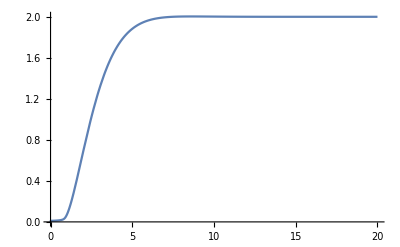

```mathematica
Plot[Evaluate[x'[t]/.sol],{t,0,20},PlotRange->All]
```

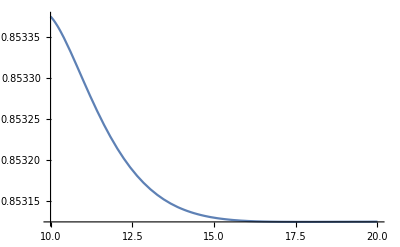

```mathematica
Plot[Evaluate[(IF x'[t])/(2τ0[t] θ0'[t]+2τ2[t] θ2'[t])//.SUBS0/.Lei//.SDATA/.sol],{t,10,20},PlotRange->All]
```

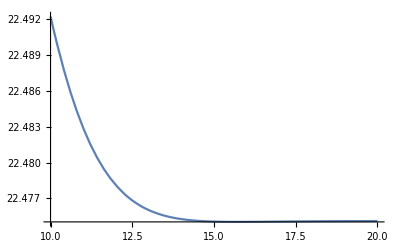

```mathematica
Plot[Evaluate[(τ0[t] θ0'[t])/735.5//.SUBS0/.Lei//.SDATA/.sol],{t,10,20},PlotRange->All]
```

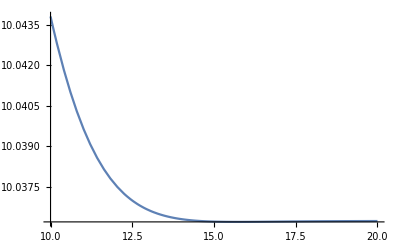

```mathematica
Plot[Evaluate[(τ2[t] θ2'[t])/735.5//.SUBS0/.Lei//.SDATA/.sol],{t,10,20},PlotRange->All]
```

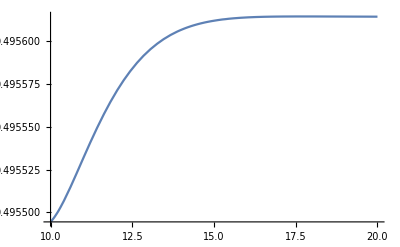

```mathematica
Plot[Evaluate[(NT0+NT2)/(W0+W2)//.SUBS0/.Lei//.SDATA/.sol],{t,10,20},PlotRange->All]
```

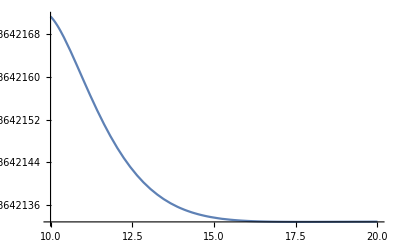

```mathematica
Plot[Evaluate[TE0//.SUBS0/.Lei//.SDATA/.sol],{t,10,20},PlotRange->All]
```

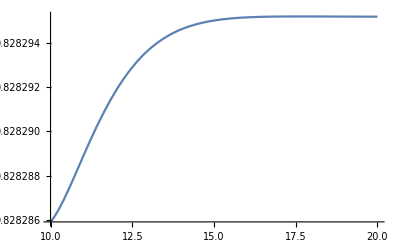

```mathematica
Plot[Evaluate[TE2//.SUBS0/.Lei//.SDATA/.sol],{t,10,20},PlotRange->All]
```

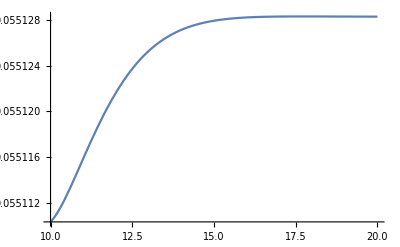

```mathematica
Plot[Evaluate[s0//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

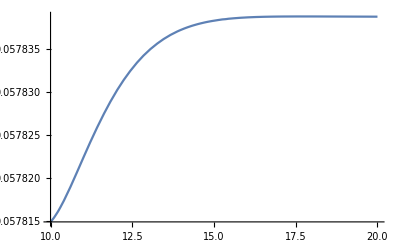

```mathematica
Plot[Evaluate[s2//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

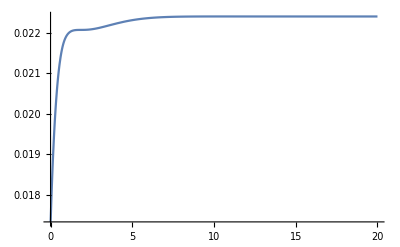

```mathematica
Plot[Evaluate[δ//.SDATA/.sol],{t,0,20},PlotRange->All]
```

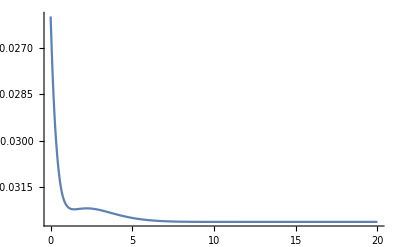

```mathematica
Plot[Evaluate[(y[t]-r3-Δy2-yc)//.SDATA/.sol],{t,0,20},PlotRange->All]
```

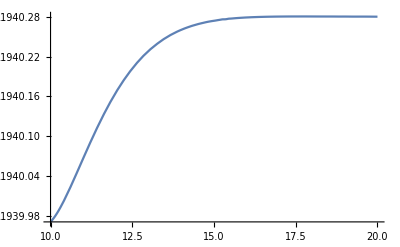

```mathematica
Plot[Evaluate[W0//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

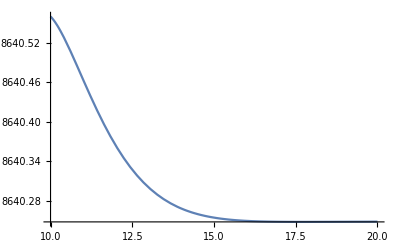

```mathematica
Plot[Evaluate[W2//.SDATA/.sol],{t,10,20},PlotRange->All]
```

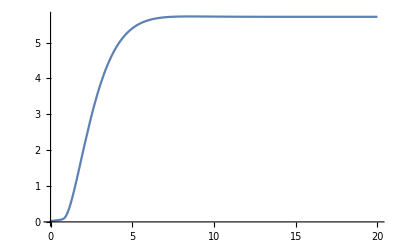

```mathematica
Plot[Evaluate[θ0'[t]/.sol],{t,0,20},PlotRange->All]
```

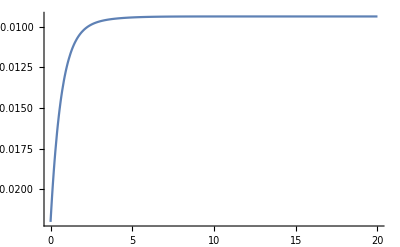

```mathematica
Plot[Evaluate[( Y[0]-r1)//.SDATA/.sol],{t,0,20},PlotRange->All]
```

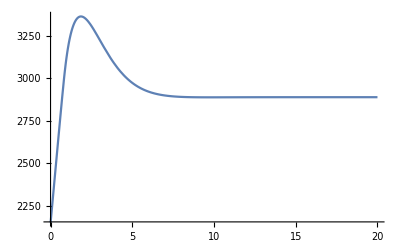

```mathematica
Plot[Evaluate[τ0[t]/.Lei//.SDATA/.sol],{t,0,20},PlotRange->All]
```

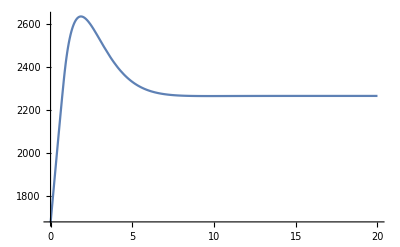

```mathematica
Plot[Evaluate[τ2[t]/.Lei//.SDATA/.sol],{t,0,20},PlotRange->All]
```

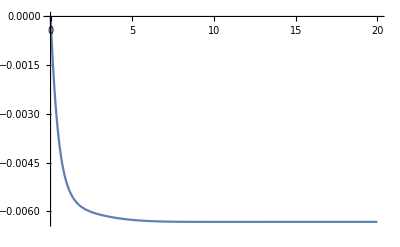

```mathematica
Plot[Evaluate[α[t]/.sol],{t,0,20},PlotRange->All]
```

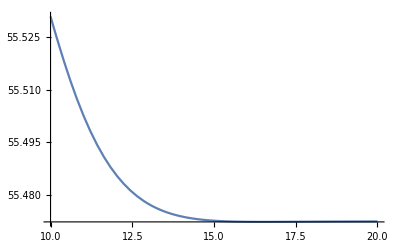

```mathematica
Plot[Evaluate[(IF x'[t])/735.5//.SDATA/.sol],{t,10,20},PlotRange->All]
```

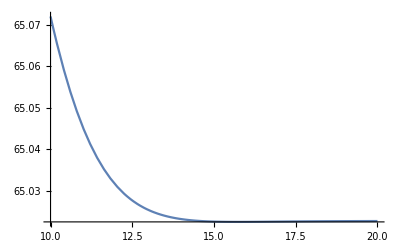

```mathematica
Plot[Evaluate[(2τ0[t] θ0'[t]+2τ2[t] θ2'[t])/735.5/.Lei//.SDATA/.sol],{t,10,20},PlotRange->All]
```

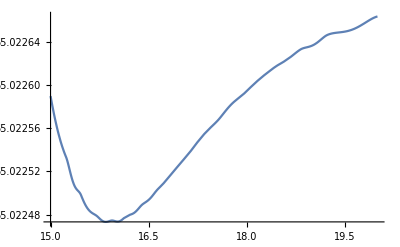

```mathematica
Plot[Evaluate[(2GT0 r1 θ0'[t]+2GT2 (r3-δ) θ2'[t])/735.5//.SUBS0/.Lei//.SDATA/.sol],{t,15,20},PlotRange->All]
```

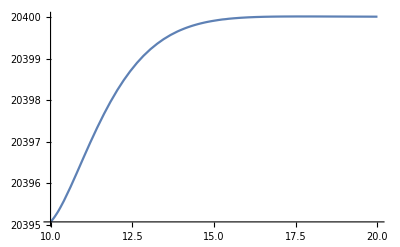

```mathematica
Plot[Evaluate[2NT0+2NT2//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

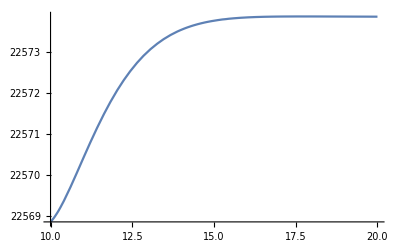

```mathematica
Plot[Evaluate[2GT0+2GT2//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

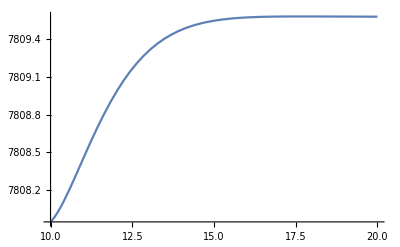

```mathematica
Plot[Evaluate[GT0//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

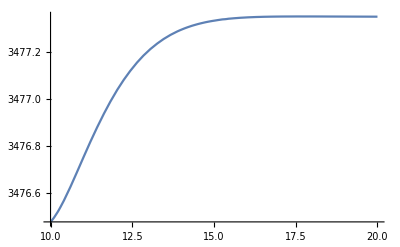

```mathematica
Plot[Evaluate[GT2//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

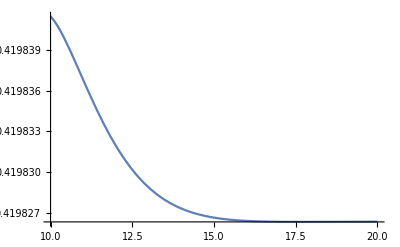

```mathematica
Plot[Evaluate[W2/(W0+W2)//.SUBS0//.SDATA/.sol],{t,10,20},PlotRange->All]
```

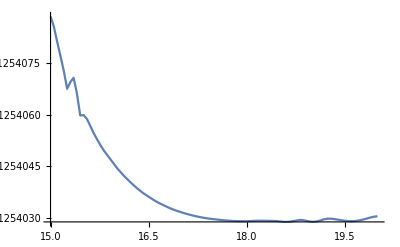

```mathematica
Plot[Evaluate[(NT0+NT2)/(GT0/(1-s0)+GT2/(1-s2))//.SUBS0/.Lei//.SDATA/.sol],{t,15,20},PlotRange->All]
```

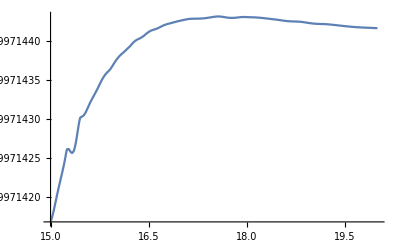

```mathematica
Plot[Evaluate[NT2/(NT0+NT2)//.SUBS0/.Lei//.SDATA/.sol],{t,15,20},PlotRange->All]
```